```mathematica
ClearAll["Global`*"]
currentDirectory=NotebookDirectory[];


R20800=25; (*can be changed based on experimental inputs*)
R20600=20;(*can be changed based on experimental inputs*)
(*lit of kex in s-1 values to be simulated*)
kexsim={10000};

(*NUCPMG frequencies*)
ν={100,500,1000,2000,3000,4000,5000,6000,7000,8000,9000,10000,11000,12000,13000,14000,15000,16000,17000,18000,19000,20000,21000,22000,23000,24000,25000,26000,27000,28000,29000,30000}; (*for linear scheme of nucpmg points*)
v = 100;

(*mag field*)(*change it for N or depending on your magnets*)
field800=800;
field600=600;

(*population of state B for simulation, max is 1*)
pBsim={0.05};
(*csd to be simulatied in ppm*)
csdsim={0.5};

err600sim=0.6;
err800sim=0.8;
(*number of replicas to run with diffent stocahstic errors*)
rep = 1;

R2val800={};
R2val600={};
kexValue={};
kABValue={};
kBAValue={};
pfValue = {};

Do[
replica =rep[[l]];
Do [csdx = csdsim[[k]];
Do[pBx = pBsim[[j]];
(*Print[pBx];*)
Do[kAB=kexsim[[i]]*(1-pBx);
kBA=kexsim[[i]]*pBx;
pf = pBx*(1-pBx)*4*π^2*csdx*csdx;
(*Print[pf];*)
AppendTo[pfValue,pf];
AppendTo[kexValue,kexsim[[i]]];
AppendTo[kABValue,kAB];
AppendTo[kBAValue,kBA];
AppendTo[simKexBM,{csdx,pBx,kexsim[[i]],pf,kAB,kBA}],
{i,Length[kexsim]}],{j,Length[pBsim]}],{k,Length[csdsim]}];

subfolder=FileNameJoin[{currentDirectory,ToString[replica]}];
If[!DirectoryQ[subfolder],CreateDirectory[subfolder]];

filename="BM_datagen_kex_pf_kAB_kBA4_"<>ToString[replica]<>".csv";
filepath=FileNameJoin[{subfolder,filename}];

(*Export[filepath,simKexBM,"CSV","TableHeadings"->None]*),
{l,Length[rep]}]


simKexBM;
kexValue;
kABValue;
kBAValue;
```

```mathematica
modelBM[ν_?NumberQ,kAB_?NumberQ,kBA_?NumberQ,R20_?NumberQ,csd_?NumberQ,field_?NumberQ]:=Block[{delta,ncp,tcp,domega,Alist,eA,Astar,eAstar,matB,matC,pB,M0,MT},delta=(4 ν)^-1;
tcp=0.06; (*decided based on experimental time*)
ncp=tcp*ν;
domega=csd*2*π*field;
Alist={{-R20-kAB,kBA},{kAB,-R20-kBA+I domega}};
eA=MatrixExp[N[Alist*delta]];
Astar=Conjugate[Alist];
eAstar=MatrixExp[N[Astar*delta]];
matB=Dot[Dot[Dot[eA,eAstar],eAstar],eA];
matC=MatrixPower[N[matB],ncp];
pB=kAB/(kAB+kBA);
M0={{1-pB},{pB}};
MT=Dot[matC,M0];
Re[(-1/(4*ncp*delta))*Log[MT[[1,1]]/M0[[1,1]]]] (*For slow exchange*)];
```

```mathematica
r2val800Table={};

(*Populate the tables with nu,r2val800,and r2val600 values*)
Do[
replica = rep[[l]];
Print[replica];
Do[csdx = csdsim[[k]];
Do[pBx = pBsim[[j]];
Do[kAB=kexsim[[i]]*(1-pBx);
kBA=kexsim[[i]]*pBx;
prefac=pBx*(1-pBx)*4*π^2*csdx*csdx;
(*Print[prefac];*)
nuList={};
r2val800List={};
r2val600List={};
Do[result800=modelBM[νvalue,kBA,kAB,R20=R20800,csdx,field800];
resultv=modelBM[v,kBA,kAB,R20=R20800,csdx,field800];
err800sim2=(resultv-R20800)*5/100; (*5% error of (max-min) introduced for 800 dataset*)
noise800=RandomVariate[NormalDistribution[0,err800sim2]];
result600=modelBM[νvalue,kBA,kAB,R20=R20600,csdx,field600];
resultv=modelBM[v,kBA,kAB,R20=R20600,csdx,field600];
err600sim2=(resultv-R20600)*5/100; (*5% error (max-min) introduced for 600 dataset*)
noise600=RandomVariate[NormalDistribution[0,err600sim2]];
AppendTo[nuList,νvalue];
AppendTo[r2val800List,result800+noise800];
AppendTo[r2val600List,result600+noise600];,{νvalue,ν}];
AppendTo[r2val800Table,<|"rep"->replica,"csdsim*10"->10csdx,"pBsim"->100pBx,"kexsim"->kexsim[[i]],"nu"->nuList,"r2val800"->r2val800List,"r2val600"->r2val600List|>];,{i,Length[kexsim]}], {j, Length[pBsim]}],{k,Length[csdsim]}],{l,rep}];
r2val600List;

currentDirectory=NotebookDirectory[];


TableForm[Table[{r2val800Table[[i,"pBsim"]],r2val800Table[[i,"kexsim"]],r2val800Table[[i,"nu"]],r2val800Table[[i,"r2val800"]],r2val800Table[[i,"r2val600"]]},{i,Length[r2val800Table]}],TableHeadings->{None,{"kexsim","nu","r2val800","r2val600"}}];
```

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

1⟦1⟧

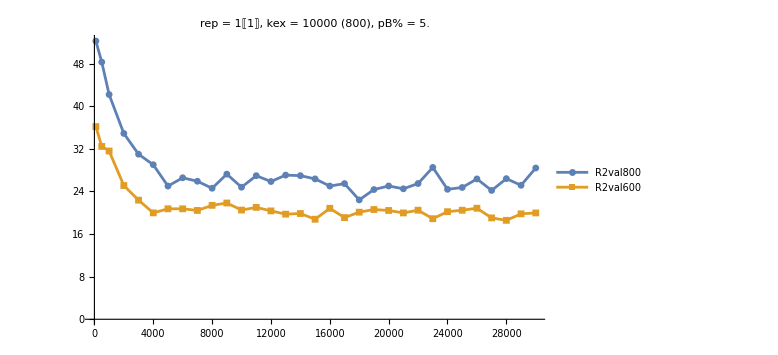

{rep,csdsim*10,pBsim,kexsim,nu,r2val800,r2val600}

```mathematica
outputFolderPath=" /Users/apurvaphale/Desktop/Apurva/CPMG_simulations/eCPMG_simulations/data_generation_BM/HCPMG/100reps/linear/data/"; (*path to save the datasets*)

plots=Table[ListLinePlot[{Tooltip[Transpose[{r2val800Table[[i]]["nu"],r2val800Table[[i]]["r2val800"]}],StringForm["kexsim = `` (800)",r2val800Table[[i]]["kexsim"]]],Tooltip[Transpose[{r2val800Table[[i]]["nu"],r2val800Table[[i]]["r2val600"]}],StringForm["kexsim = `` (600)",r2val800Table[[i]]["kexsim"]]]},PlotMarkers->{Automatic,Small},FrameLabel->{"nu","R2eff"},PlotRange->All,Joined->True,ImageSize->Large,PlotLabel->StringForm[      "rep = ``, kex = `` (800), pB% = ``",r2val800Table[[i]]["rep"],r2val800Table[[i]]["kexsim"],r2val800Table[[i]]["pBsim"]],PlotLegends->{"R2val800","R2val600"}],{i,Length[r2val800Table]}];


Do[dataset=Transpose[{r2val800Table[[i]]["nu"],r2val800Table[[i]]["r2val800"],r2val800Table[[i]]["r2val600"]}];
kexValue=IntegerString[Round[r2val800Table[[i]]["kexsim"]],10,6];
pBValue=IntegerString[Round[r2val800Table[[i]]["pBsim"]],10,2];
csdValue=IntegerString[Round[r2val800Table[[i]]["csdsim*10"]],10,2];
replica=ToString[r2val800Table[[i]]["rep"]];
subfolder=FileNameJoin[{currentDirectory,replica}];
If[!DirectoryQ[subfolder],CreateDirectory[subfolder]];
outputFileName=FileNameJoin[{subfolder,StringJoin["csd+",csdValue,"+kex+",kexValue,"+pB+",pBValue,"+fromBM.csv"]}];
Export[outputFileName,dataset,"CSV"];,{i,Length[r2val800Table]}]



Column[plots]
Keys[r2val800Table[[1]]]
```